# You Drank, but can you Drive?

Ruhi Shah

Recently, I visited the United Kingdom, which is where the inspiration for this essay comes from. Boy, do people drink there! I was at a very famous pub in Oxford, called Turf Tavern (where allegedly, an Australian Prime Minster broke a Guinness World Record chugging ale). Here, I witnessed an interesting conversation. Two gentlemen were talking about getting home. “I can drive in a little bit when I’ve sobered up.” he said, and that got me thinking. Exactly how long would it take that particular gentleman to “sober up” enough to be able to drive safely. I decided to create this for anyone to decide how long it would take. People at bars generally don’t know the exact amount of alcohol they have consumed, so I decided to search the Wolfram Food directory for common alcoholic beverages, here are some popular drinks:

```mathematica
alcoholicDrinks={Entity["Food","Martini::c6h98"],Entity["Food","VanillaExtract::6g22f"],Entity["Food","BloodyMary::328gx"],Entity["Food","Brandy::q5447"],Entity["Food","Vermouth::679s2"],Entity["Food","Cognac::y9462"],Entity["Food","BeerRegular::8x3f9"], Entity["Food","EggNog::3dwyy"],Entity["Food","WineMulled::2t398"],
Entity["Food","CiderAverage::5dtvm"],Entity["Food","GinTonic::n5779"],Entity["Food","Sangria::xmm5b"],Entity["Food","Rum::889s3"],Entity["Food","Tequila::nb2x5"],Entity["Food","AlcoholicBeveragePinaColadaCanned::vv7h8"],Entity["Food","IrishCoffee::6pv9d"],Entity["Food","WineRed::qxm3p"]}
```

{Martini,Vanilla extract,Bloody mary,Brandy,Vermouth,Cognac,Beer, regular,Egg nog,Wine mulled,Cider (average),Gin tonic,Sangria,Rum,Tequila,Alcoholic beverage, pina colada, canned,Irish Coffee,Wine, red}

These were “Food” entities in the Wolfram Language that have been recently updated (In version 11, there is information on over 40,000 foods). I used the EntityProperty function to extract the food items that have the most amount of alcohol. I then manually selected the drinks that the internet considered to be the most popular. To find the amount of alcohol in each, I used the property “AlcoholContentPerServing” which gave the alcohol content in grams for each typical serving size. I visualized it using a bar graph as well.

<|Martini→28.7 g,Vanilla extract→1.4448 g,Bloody mary→10.5 g,Brandy→32. g,Vermouth→12. g,Cognac→32. g,Beer, regular→4. g,Egg nog→3.7 g,Wine mulled→2.8 g,Cider (average)→2.7 g,Gin tonic→4. g,Sangria→5.6 g,Rum→39.7 g,Tequila→38. g,Alcoholic beverage, pina colada, canned→2.934 g,Irish Coffee→5.6 g,Wine, red→9.9 g|>

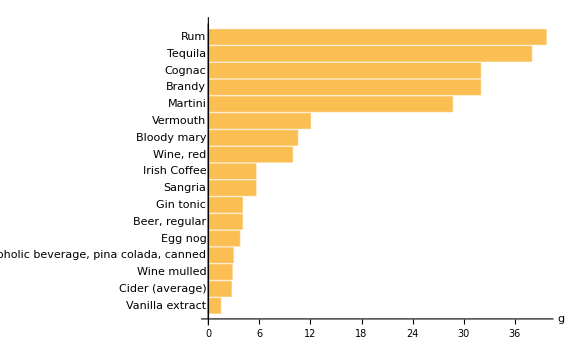

```mathematica
alcoholicContent = EntityValue[alcoholicDrinks,"AlcoholContentPerServing","EntityAssociation"]
BarChart[Sort[alcoholicContent], ChartLabels->Automatic,AxesLabel->Automatic, BarOrigin-> Left, ImageSize->Large]
```

In order to drink and then drive, you need to have BAC (Blood Alcohol Content) below 0.08%. This value still seems a little high to me, even at 0.08%, there are several prominent effects of alcohol. Even more surprising was the value in Canada, which was 0.15%. About 40% causes death, just for reference. To calculate BAC, you need a couple of things. I used the “Quantity” feature in Wolfram Language to assign units to my values throughout this essay. Here is my information, with units (feel free to replace it with yours):

```mathematica
$AllowedBAC = 0.08;

bodyweight = Quantity[100, "Pounds"];
gender = "female";
```

To figure out how much I can drink for each specific drink and still drive, I can do the following, where howManyDrinks is a function, for which the definition appears later. Oh no! I can only drink 22 servings of vanilla extract! That is good to know.

```mathematica
howManyDrinks[bodyweight_,drinktype_,gender_]:= Quantity[Floor[($AllowedBAC*QuantityMagnitude@bodyweight*If[gender==="male",0.73,0.66])/(QuantityMagnitude@drinktype*5.14*0.035274)],"drinks"]
numberofdrinksGeneral=AssociationThread[Keys[alcoholicContent],howManyDrinks[bodyweight,#,gender]&/@Values[alcoholicContent]]
```

<|Martini→1 drink,Vanilla extract→20 drinks,Bloody mary→2 drinks,Brandy→0 drinks,Vermouth→2 drinks,Cognac→0 drinks,Beer, regular→7 drinks,Egg nog→7 drinks,Wine mulled→10 drinks,Cider (average)→10 drinks,Gin tonic→7 drinks,Sangria→5 drinks,Rum→0 drinks,Tequila→0 drinks,Alcoholic beverage, pina colada, canned→9 drinks,Irish Coffee→5 drinks,Wine, red→2 drinks|>

I also need some information on how much I’ve been drinking and what I’ve been drinking. The type of drink can be entered using free-form input (just type it in after ctrl+=), or the entity can easily be copy-pasted from anywhere above.

```mathematica
drinktype = Entity["Food","Martini::c6h98"];
numberofdrinks = Quantity[3,"drinks"];
timepassed = Quantity[1,"hour"];
```

Now, with that information lets find out if you can drive! calculateBAC is a function that takes in the previous parameters and figures out the BAC level. canIDriveQ answers our question.

```mathematica
calculateBAC[bodyweight_,drinktype_, numberofdrinks_,gender_,timepassed_]:= -;
canIDriveQ[bac_]:= ;
BAC = calculateBAC[bodyweight,drinktype, numberofdrinks, gender, timepassed];
canIDriveQ[BAC]
```

No

Okay, now you realize you can’t drive. How long should you wait until you can? howMuchLonger is a function that lets you know.

```mathematica
howMuchLonger[bodyweight_,drinktype_, numberofdrinks_,gender_,timepassed_]:= 
howMuchLonger[bodyweight,drinktype,numberofdrinks,gender,timepassed]
```

9.435 h

Yes! It takes that long. So you think you might have “sobered up” but guess what, the breathalyzer will not. Regardless of this what this article says, drinking and driving is NOT a joke. Just call an Uber! Public Transport! Walk! Wait! Don’t drink! Its not that hard to save money, and some lives too. Also, you may not realize it, but you could still very much be under the influence. Slow reaction time, lack of coordination, reduced concentration, decreased vision, and inhibition of judgement is only a little bit of what alcohol will do to you. This is also a very common issue, alcohol-related vehicle crashes make up $44 million every year. That is $44 million that could be used for research in science! Also, if you are in high school, please do not drink and drive. In 2011, over 1 million students admitted to drinking and driving. That is just not acceptable at all. Use this tool, wait, or drink less, and be safe!